### Функции

```mathematica
ReadSnapHeader[fname_String]:=Block[{ReadTilleq,fin,t,count,np,KolProc,n1,n2,n3,Rey,a,},
ReadTilleq[stream_,type_,opts1___]:=Block[{},
		Skip[stream,Record,RecordSeparators->{"="}];Skip[stream,Character];Return[Read[stream,type,opts1]];
		];
	fin=OpenRead[fname,BinaryFormat->True];
	t = ReadTilleq[fin, Real];
	count = ReadTilleq[fin, Number];
	np = ToExpression[ReadTilleq[fin, Record, RecordSeparators->{"\n"}]];
	KolProc = Times@@np;
	n1 = ReadTilleq[fin, Number];
	n2 = ReadTilleq[fin, Number];
	n3 = ReadTilleq[fin, Number];
	Rey = ReadTilleq[fin, Real];
Close[fin];
{t,count,np,{n1,n2,n3},Rey}
	]
```

```mathematica
ReadZipSnapHeader[fname_String]:=Block[{temp,out},
name=StringReplace[fname,".zip"->""](*<>".snp"*);
temp=First[Import[fname,{"*.snp","Binary"}]];
Export[name,temp,"Binary","DataFormat"-> "Byte"];
out=ReadSnapHeader[name];
(*Close[name];*)
DeleteFile[name];
Return[out]
]
```

```mathematica
ScanSnaps:=Block[{files},
If[$ZIP===True,files=FileNames["*.snp.zip"],files=FileNames["*.snp"]];
If[Length[files]==0,Print["Файлов не найдено"];Return[{}]];
If[$ZIP===True,
info=ReadZipSnapHeader/@files,
info=ReadSnapHeader/@files];
If[Length[Union[info⟦All,4⟧]]==1,
Print["Сетка одинаковая: ",info⟦1,4⟧];
If[Length[Union[info[[All,3]]]]==1,
Print["Деление на процессы одинаковое: ",info⟦1,3⟧];
Print["Структура у всех одинаковая"];Return[info⟦All,{1,2,5}⟧],
Print["\tДля деления ",#," есть снимки:\n",info⟦First/@Position[info,#],{1,2,5}⟧]&/@Union[info[[All,3]]];],
Map[Function[mesh,
If[Length[Union[info[[First/@Position[info,mesh],3]]]]==1,
Print["Для сетки ",mesh," деление на процессы одинаковое: ",info⟦Position[info,mesh]⟦1,1⟧,3⟧, " и есть снимки:\n",info⟦First/@Position[info,mesh],{1,2,5}⟧],
Print["Для сетки ",mesh," есть несколько делений на процессы:"];
Print["\tДля деления ",#," есть снимки:\n",info⟦Intersection[First/@Position[info,mesh],First/@Position[info,#]],{1,2,5}⟧]&/@Union[info[[All,3]]]
]
],Union[info[[All,4]]]
];
];
Transpose[info]
]
```

### Процесс

```mathematica
ReadZipSnapHeader["screw_64_1020.snp.zip"]
```

```mathematica
ReadSnapHeader["screw_2_187.snp"]
```

```mathematica
$ZIP=False;
```

```mathematica
infos=SortBy[ScanSnaps,#⟦2⟧&]
```

Сетка одинаковая: {32,32,32}

Деление на процессы одинаковое: {1,2,2}

Структура у всех одинаковая

{{10.0017,1402,10.},{10.0017,1402,10.},{10.0017,1402,10.},{10.0017,1402,10.},{20.0054,2817,20.},{20.0054,2817,20.},{20.0054,2817,20.},{20.0054,2817,20.},{30.005,4386,30.},{30.005,4386,30.},{30.005,4386,30.},{30.005,4386,30.},{40.0032,6160,40.},{40.0032,6160,40.},{40.0032,6160,40.},{40.0032,6160,40.},{50.0006,8379,50.},{50.0006,8379,50.},{50.0006,8379,50.},{50.0006,8379,50.},{60.0002,11064,60.},{60.0002,11064,60.},{60.0002,11064,60.},{60.0002,11064,60.},{70.002,14222,70.},{70.002,14222,70.},{70.002,14222,70.},{70.002,14222,70.},{80.0015,17862,80.},{80.0015,17862,80.},{80.0015,17862,80.},{80.0015,17862,80.},{90.0015,21999,90.},{90.0015,21999,90.},{90.0015,21999,90.},{90.0015,21999,90.},{100.,26622,100.},{100.,26622,100.},{100.,26622,100.},{100.,26622,100.}}

```mathematica
Union[Last/@infos]
```

{10.,20.,30.,40.,50.,60.,70.,80.,90.,100.}

```mathematica
Position[infos,{_,_,#},1]⟦-1⟧&/@Union[Last/@infos]
```

{{4},{8},{12},{16},{20},{24},{28},{32},{36},{40}}

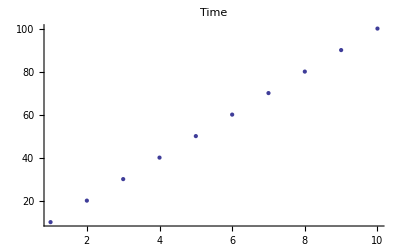
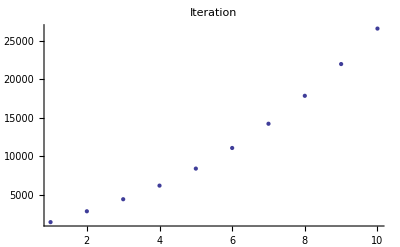
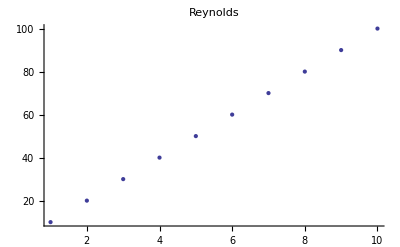

```mathematica
MapThread[ListPlot[#1,PlotLabel->#2]&,{CutList[Union[infos]ᵀ,100],{"Time","Iteration","Reynolds"}}]
```

```mathematica
info1=infos;
```

```mathematica
Intersection[infos,info1]//Length
```

0

```mathematica
dellist=Complement[infos[[All,2]],#⟦2⟧&/@Extract[infos,Position[infos,{_,_,#},1]⟦-1⟧&/@Union[Last/@infos]]]
```

{132,199,266,332,399,466,533,599,666,733,800,867,934,1001,1068,1135,1202,1269,1335,1547,1614,1679,1748,1815,1881,1948,2014,2081,2148,2215,2282,2349,2416,2483,2549,2616,2683,2750,2965,3041,3117,3192,3267,3340,3416,3490,3564,3637,3711,3786,3862,3936,4010,4084,4159,4236,4311,4564,4647,4732,4817,4901,4985,5069,5154,5237,5321,5405,5490,5573,5657,5740,5824,5908,5992,6076,6383,6490,6596,6701,6805,6910,7014,7119,7224,7329,7434,7539,7644,7749,7854,7959,8064,8169,8274,8622,8750,8877,9004,9132,9261,9390,9519,9648,9776,9905,10034,10163,10292,10420,10549,10678,10807,10936,11357,11512,11662,11812,11963,12113,12264,12415,12565,12716,12866,13017,13168,13318,13469,13619,13770,13921,14071,14542,14720,14894,15068,15242,15417,15591,15766,15941,16115,16290,16465,16639,16814,16989,17163,17338,17513,17687,18216,18413,18612,18810,19009,19208,19407,19607,19806,20005,20205,20404,20604,20803,21002,21202,21401,21600,21800,22392,22618,22840,23062,23284,23507,23730,23952,24174,24397,24620,24842,25065,25287,25510,25732,25955,26177,26400}

```mathematica
dellist=Complement[infos[[All,2]],CutList[infos[[All,2]],100]];
```

```mathematica
DeleteFile["ponom_3_"<>PadLeft[Characters@ToString[#],5,"0"]<>".snp"]&/@dellist;
```